```mathematica
f[x_]:= 2*x-Power[x,4];

n=5;
h = 1.0/n;
```

```mathematica
fValues=Table[f[i*h],{i,0,n}];
fValues[[1]]=0;
M=ConstantArray[0,{n+1,n+1}];
M[[1,1]] = 1;
M[[n+1,n+1]] = 1;
Do[M[[i,i]]=2;
If[i>1 ,M[[i,i-1]]=-1];
If[i<n+1,M[[i,i+1]]=-1];,{i,2,n}];
b=fValues*h^2
MatrixForm[M]
```

{0.,0.015936,0.030976,0.042816,0.047616,0.04}

(1 | 0 | 0 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0
0 | -1 | 2 | -1 | 0 | 0
0 | 0 | -1 | 2 | -1 | 0
0 | 0 | 0 | -1 | 2 | -1
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
U = LinearSolve[M, b]
```

{0.,0.065984,0.116032,0.135104,0.11136,0.04}

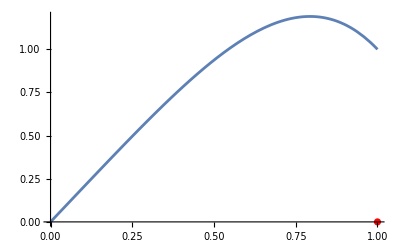

```mathematica
p1= Plot[f[x], {x, 0,1}];
p2 = ListPlot[U, PlotStyle->Red, PlotRange-> Automatic];
Show[p1, p2]
```